```mathematica
SetDirectory["/home/ehteqx/Scaricati/simulazione"]
```

/home/ehteqx/Scaricati/simulazione

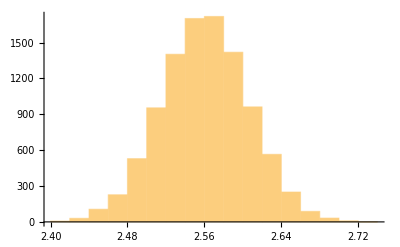

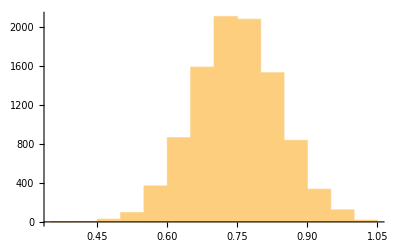

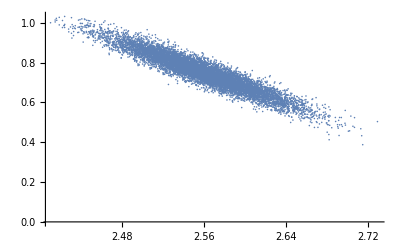

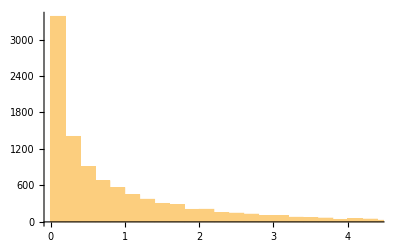

```mathematica
ClearAll[temp0, temp1, istogm, istogq, punto, istogx];
temp0 = Import["results.dat"];
temp1 = Transpose[temp0];
istogm = temp1[[2]];
istogq = temp1[[3]];
istogx = temp1[[4]];
Histogram[istogm]
Histogram[istogq]
punto = Transpose[{istogm, istogq}];
ListPlot[punto]
Histogram[istogx]
```